# Finite-size BBM92 protocol

DESCRIPTION: Implementing the finite key BBM92 protocol. Improve existing key rates by using an updated sampling bound to replace previous use of the Serfling bound. 

Analysis based on:
Security Analysis of Quantum Key Distribution with Small Block Length and Its Application to Quantum Space Communications, Lim, Xu, Pan, Ekert, Phys. Rev. Lett. 126 (2021).

Date: 07th June 2024
Author: Jasminder Sidhu

```mathematica
Clear["Global`*"]
```

```mathematica
(*Define the log function*)
h2[0|0.]=0;
h2[x_]:=-x Log2[x]-(1-x) Log2[1-x];
SetAttributes[h2,Listable]

(*Define constants and functions*)
δ=0.0455;
s=6;
r=1.19 h2[δ];

(*Definitions and functions*)
k[β_,m_]:=Floor[β m]; 
n[β_,m_]:=m-k[β,m];
t[s_]:=-Log2[10^(- (s+2))];
Γ[x_,m_]:= 1/(x+1) + 1/(m-x+1);
ϵpe[β_, ν_, ξ_, m_]:= (Exp[-(2m k[β,m] ξ^2)/(n[β,m]+1)]+Exp[-2 Γ[m (δ + ξ),m] (n[β,m]^2 (ν - ξ)^2 - 1)])^(1/2);
ϵpa[β_,ν_,m_,l_]:= 1/2 √(2^(-n[β,m] (1-h2[δ+ν]-r) + t[s] + l));

(*Number of samples to take for each parameter*)
betaNo = 90;
xiNo = 90;
nuNo = 90;

(*Bounding values; Emulate np.linspace of Python*)
betas = N@Subdivide[10^-6, 1/2, betaNo - 1];
xis = N@Subdivide[0, 1/2-δ, xiNo - 1];
nus = N@Subdivide[0, 1/2-δ, nuNo - 1];

(*Constraints*)
C1[l_, m_,β_, ν_, ξ_]:=10^(- (s+2))+ 2 ϵpe[β, ν, ξ, m] + ϵpa[β,ν,m,l] <= 10^-s;

FiniteRateOpt={{"FKL","FKR(alpha)","m","s","beta","nu","xi"}};
Do[
FKlengths={{"FKL","beta","nu","xi"}};
Do[
l = Log2[4 (10^-s-10^(-(s+2))-2 ϵpe[betas[[kk]], nus[[i]], xis[[j]], m])^2] +n[betas[[kk]],m] (1-h2[δ+nus[[i]]] - r)- t[s]; 
If[C1[l, m,betas[[kk]], nus[[i]], xis[[j]]], AppendTo[FKlengths, {l,betas[[kk]],nus[[i]],xis[[j]]}], Null],{kk, 1, Length[betas], 1},{j, 1, Length[xis], 1},{i, j+1, Length[nus], 1}];
FKlengths = Sort[FKlengths,#1[[1]]>#2[[1]]&][[2]];

maxLength=Max[0,FKlengths[[1]]];
beta=FKlengths[[2]];
nu=FKlengths[[3]];
xi=FKlengths[[4]];

AppendTo[FiniteRateOpt, {maxLength, maxLength/m,m,s,beta,nu,xi}],{m,3000,8000,100}];
```

General::munfl: Exp[-804.996] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-915.909] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

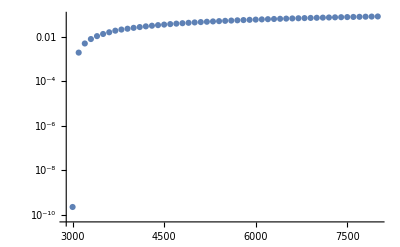

```mathematica
ListLogPlot[FiniteRateOpt[[All,{3,2}]]]
```

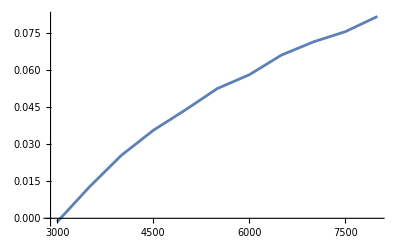

```mathematica
ListLinePlot[FiniteRateOpt[[All,{3,2}]]]
```